```mathematica
(* Run to Install FeynCalc 
<<FeynCalc` *)
```

```mathematica
Clear["Global`*"]
```

# Constructing

## Do Wick’s contractions

```mathematica
(* Define the vertex of the scalar field interacting with the metric perturbation *)
Vertex[ω_,k_,mu_,nu_]:=- 1/2(FV[k,mu]*FV[ω,nu]+FV[ω,mu]*FV[k,nu]) + (1 - 4ξ)/4*MT[mu,nu]*SP[q,q] + ξ*FV[q,mu]*FV[q,nu];

(* Rules *)
SeparateRule = {
(* separate  *)
FV[p1_+p2_,a_]:>FV[p1,a] + FV[p2,a],
FV[p1_+p2_+p3_,a_]:>FV[p1,a] + FV[p2,a]+FV[p3,a]
};

Ruleqx = {
(* separate  *)
FV[x*q,a_]:>x*FV[q,a],
FV[q*x,a_]:>x*FV[q,a],

FV[-x*q,a_]:>-x*FV[q,a],
FV[-q*x,a_]:>-x*FV[q,a],

FV[q*(x-1),a_]:>(x-1)*FV[q,a],
FV[(x-1)*q,a_]:>(x-1)*FV[q,a]
};

ruleϵL = {
(* separate  *)
FV[ϵ*l,a_]:>ϵ*FV[l,a],
FV[l*ϵ,a_]:>ϵ*FV[l,a],

(* separate  *)
SP[ϵ*l,ϵ*l] :>ϵ^2 SP[l,l],
SP[l*ϵ,l*ϵ]:>ϵ^2 SP[l,l],

SP[l,ϵ*l]:>ϵ*SP[l,l],
SP[l,l*ϵ]:>ϵ*SP[l,l],

SP[ϵ*l,l]:>ϵ*SP[l,l],
SP[l*ϵ,l]:>ϵ*SP[l,l]
};
```

```mathematica
(* Costruct the numerator *)
Vertex1= Vertex[q-l - x*q,l + x*q,μ,ν];
Vertex2 = Vertex[l + x*q-q,-l - x*q,ρ,σ];

NumeratorV = Vertex1*Vertex2;

(* with molteplicity 2 *)
Numtot=Collect2[2*NumeratorV,MT,FV] // Simplify;

NumFinal=(Numtot//.SeparateRule)//.Ruleqx // Simplify;

(* Even part *)
NumMinus = NumFinal /. l->-l;
NumEven = (NumFinal + NumMinus)/2 // Simplify;

NumFinϵ =NumEven /. l->ϵ*l;

(* The expression to working with *)
NumFin = Collect2[NumFinϵ//. ruleϵL //Simplify,MT,FV];
```

## Extract terms

```mathematica
(* Extract the costant part in D-dimension *)
zeroTerm = NumFin/. ϵ->0 // Simplify;

(* Now work with the dipendent part *)
NumL = Collect2[(NumFin - zeroTerm // Simplify),MT,FV];

(* check that it does not contain constant terms *)
Print["\n (should be zero): ",NumL /. ϵ->0]

(* Terms with 2  : *)
NumLϵ = NumL/ϵ^2//Simplify;
ϵ2Term =Collect2[NumLϵ/.ϵ->0//Simplify,MT,FV];

(* Terms with 4  :  *)
newNumL = NumL - ϵ^2 * ϵ2Term //Simplify;
newNumLϵ = newNumL/ϵ^4//Simplify;
ϵ4Term = Collect2[newNumLϵ/.ϵ->0 //Simplify,MT,FV];

(* check that we have taken all the terms *)
Print["\n (should be zero): ",(NumFin - zeroTerm - ϵ^2 ϵ2Term- ϵ^4 ϵ4Term) //Simplify]
```

(should be zero): 0

(should be zero): 0

## Integrate

```mathematica
n = 2;
d = 4 - ϵ;

Δ= x(x-1)SP[q,q] + m^2;
```

```mathematica
S[mu_,nu_,rho_,sigma_]:=MT[mu,nu]*MT[rho,sigma] + MT[mu,rho]*MT[nu,sigma] + MT[mu,sigma]*MT[nu,rho];
(* substitute  *)
RuleS ={
FV[l,a_]*FV[l,b_]*FV[l,c_]*FV[l,d_]:>S[a,b,c,d]
};
```

```mathematica
I4 = (-1)^n Simplify[Normal[Series[Gamma[n-d/2- 2]/Gamma[n] Δ^(d/2+2-n)/(4π)^(d/2),{ϵ,0,0}]]];

term4 = ϵ4Term//.RuleS //Simplify;
I4term = I4*1/4*term4;
```

```mathematica
(* substitute  *)
Ruleη = {
FV[l,a_]*FV[l,b_]:>MT[a,b]
};
```

```mathematica
I2 = (-1)^(n-1)  Simplify[Normal[Series[Gamma[n-d/2- 1]/Gamma[n] Δ^(d/2+1-n)/(4π)^(d/2),{ϵ,0,0}]]];
term2 =ϵ2Term//.Ruleη//Simplify;
I2term = I2*1/2*term2;
```

```mathematica
Int[α_]:= (-1)^(n+α) Simplify[Normal[Series[(Gamma[n-d/2- α]Gamma[d/2+ α])/(Gamma[n]Gamma[d/2]) Δ^(d/2+α-n)/(4π)^(d/2),{ϵ,0,0}]]];
```

```mathematica
I0term = Int[0]*zeroTerm;
```

```mathematica
(* The result after integration in  *)
FinalResult = I4term +I2term +  I0term  // Simplify;
```

## Take the Imaginary part: sub

```mathematica
subLog = FinalResult/. Log[(-1+x) x SP[q,q]+m^2]->Log[z];
divLog = subLog/Log[z];
limRes = Limit[Limit[divLog,{z->∞}],{ϵ->0}];
resfin = π*limRes // Simplify;
```

## Final result

```mathematica
x1 = 1/2-1/2 √((-4 m^2+SP[q,q])/SP[q,q]) ;
x2 = 1/2+1/2 √((-4 m^2+SP[q,q])/SP[q,q]);
ΠMassive = Integrate[resfin,{x,x1,x2}] // Simplify;
ΠMassless = Collect2[ΠMassive/.m->0 //Simplify,MT,FV];
ΠConf = Collect2[ΠMassless/.ξ->1/6 //Simplify,MT,FV];
ΠMinimal = Collect2[ΠMassless/. ξ->0//Simplify, MT,FV];
```

## Check Massless case: Real and Imaginary part of the Tensor

```mathematica
serieResult = Series[(FinalResult/.m->0)//Simplify,{ϵ,0,0}];
NoPolesPart = SeriesCoefficient[serieResult,0];
TensorIntegralFinal = Integrate[NoPolesPart,{x,0,1}];

(* Assume  *)
TensorFinal = Simplify[TensorIntegralFinal,Assumptions->SP[q,q]>0];

subX = TensorFinal/.{Log[-SP[q,q]]->X,Log[-SP[q,q]/(4 π)]->X - Log[4π]} //Simplify;
(* when  has  the imaginary part is  *)
Imtens = subX/. X->-ⅈ*π //Simplify;

(* Look at the expression and extract by hand the imaginary part, which we define in the next step
Imtensnew = Collect[Imtens,π] //StandardForm *)
```

```mathematica
(* the part proportional to ⅈ *)
ImT = 1/(28800 π)(120 ⅈ (1-10 ξ+30 ξ^2) FV[q,μ] FV[q,ν] FV[q,ρ] FV[q,σ]-60 ⅈ (-1+5 ξ) FV[q,ρ] FV[q,σ] MT[μ,ν] SP[q,q]-150 ⅈ (-1+4 ξ) (-1+6 ξ) FV[q,ρ] FV[q,σ] MT[μ,ν] SP[q,q]-15 ⅈ FV[q,ν] FV[q,σ] MT[μ,ρ] SP[q,q]-15 ⅈ FV[q,μ] FV[q,σ] MT[ν,ρ] SP[q,q]+15 ⅈ FV[q,ρ] (-FV[q,ν] MT[μ,σ]-FV[q,μ] MT[ν,σ]) SP[q,q]-60 ⅈ (-1+5 ξ) FV[q,μ] FV[q,ν] MT[ρ,σ] SP[q,q]-150 ⅈ (-1+4 ξ) (-1+6 ξ) FV[q,μ] FV[q,ν] MT[ρ,σ] SP[q,q]-150 ⅈ MT[μ,ν] MT[ρ,σ] SP[q,q]^2+600 ⅈ ξ MT[μ,ν] MT[ρ,σ] SP[q,q]^2+225 ⅈ (-1+4 ξ)^2 MT[μ,ν] MT[ρ,σ] SP[q,q]^2+15 ⅈ (MT[μ,σ] MT[ν,ρ]+MT[μ,ρ] MT[ν,σ]+MT[μ,ν] MT[ρ,σ]) SP[q,q]^2);
```

```mathematica
(* Take the imaginary part by dividing with -ⅈ *)
ΠTensorMassless2 = Collect2[(-ImT/ⅈ //Simplify)/.SP[q,q]->Pair[Momentum[q],Momentum[q]],MT,FV];

Print["\n (should be zero): ",ΠTensorMassless2-ΠMassless/.SP[q,q]->Pair[Momentum[q],Momentum[q]] //Simplify]
```

(should be zero): 0

## Check Ward Identity

```mathematica
Print["\n (should be zero): ",Contract[ΠMassive*FV[q,μ]]//Simplify]
Print["\n (should be zero): ",Contract[ΠMassless*FV[q,μ]]//Simplify]
```

(should be zero): 0

(should be zero): 0

## Check Traceless (for conformally coupled)

```mathematica
Print["\n (should be zero): ",Contract[MT[μ,ν]*ΠConf]//Simplify]
```

(should be zero): 0

## Check for conformally coupled field () to the known result

```mathematica
πtens[mu_,nu_]:= FV[q,mu]*FV[q,nu] -MT[mu,nu]*SP[q,q];

Πtens = 2*πtens[μ,ν]*πtens[ρ,σ] - 3*πtens[μ,ρ]*πtens[ν,σ] - 3*πtens[μ,σ]*πtens[ν,ρ];

ResultΠ = (4/3)/(7680 π^2)*Πtens*π //Simplify;

Print["\n (should be zero): ",ΠConf - ResultΠ//Simplify]
```

(should be zero): 0

```mathematica
(* Print of the results *)
Print["\n Massive = ",Collect2[ΠMassive,MT,FV]]
Print["\n Massless = ",ΠMassless]
Print["\n Conformal = ",ΠConf]
Print["\n Minimally = ",ΠMinimal]
```

Massive = -((ḡ)^μσ (ḡ)^νρ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π)-((ḡ)^μρ (ḡ)^νσ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π)+((q̄)^ν (q̄)^σ (ḡ)^μρ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π (q̄)^2)+((q̄)^ν (q̄)^ρ (ḡ)^μσ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π (q̄)^2)+((q̄)^μ (q̄)^σ (ḡ)^νρ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π (q̄)^2)+((q̄)^μ (q̄)^ρ (ḡ)^νσ √(((q̄)^2-4 m^2)/(q̄)^2) (4 m^2-(q̄)^2)^2)/(1920 π (q̄)^2)-((q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ √(((q̄)^2-4 m^2)/(q̄)^2) (6 m^4-20 ξ (q̄)^2 m^2+2 (q̄)^2 m^2+30 ξ^2 (q̄)^4-10 ξ (q̄)^4+(q̄)^4))/(240 π (q̄)^4)-((ḡ)^μν (ḡ)^ρσ √(((q̄)^2-4 m^2)/(q̄)^2) (8 m^4-80 ξ (q̄)^2 m^2+16 (q̄)^2 m^2+120 ξ^2 (q̄)^4-40 ξ (q̄)^4+3 (q̄)^4))/(960 π)+((q̄)^ρ (q̄)^σ (ḡ)^μν √(((q̄)^2-4 m^2)/(q̄)^2) (8 m^4-80 ξ (q̄)^2 m^2+16 (q̄)^2 m^2+120 ξ^2 (q̄)^4-40 ξ (q̄)^4+3 (q̄)^4))/(960 π (q̄)^2)+((q̄)^μ (q̄)^ν (ḡ)^ρσ √(((q̄)^2-4 m^2)/(q̄)^2) (8 m^4-80 ξ (q̄)^2 m^2+16 (q̄)^2 m^2+120 ξ^2 (q̄)^4-40 ξ (q̄)^4+3 (q̄)^4))/(960 π (q̄)^2)

Massless = -((ḡ)^μσ (ḡ)^νρ (q̄)^4)/(1920 π)-((ḡ)^μρ (ḡ)^νσ (q̄)^4)/(1920 π)-((120 ξ^2-40 ξ+3) (ḡ)^μν (ḡ)^ρσ (q̄)^4)/(960 π)+((120 ξ^2-40 ξ+3) (q̄)^ρ (q̄)^σ (ḡ)^μν (q̄)^2)/(960 π)+((q̄)^ν (q̄)^σ (ḡ)^μρ (q̄)^2)/(1920 π)+((q̄)^ν (q̄)^ρ (ḡ)^μσ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^σ (ḡ)^νρ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^ρ (ḡ)^νσ (q̄)^2)/(1920 π)+((120 ξ^2-40 ξ+3) (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2)/(960 π)-((30 ξ^2-10 ξ+1) (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ)/(240 π)

Conformal = -((ḡ)^μσ (ḡ)^νρ (q̄)^4)/(1920 π)-((ḡ)^μρ (ḡ)^νσ (q̄)^4)/(1920 π)+((ḡ)^μν (ḡ)^ρσ (q̄)^4)/(2880 π)-((q̄)^ρ (q̄)^σ (ḡ)^μν (q̄)^2)/(2880 π)+((q̄)^ν (q̄)^σ (ḡ)^μρ (q̄)^2)/(1920 π)+((q̄)^ν (q̄)^ρ (ḡ)^μσ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^σ (ḡ)^νρ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^ρ (ḡ)^νσ (q̄)^2)/(1920 π)-((q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2)/(2880 π)-((q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ)/(1440 π)

Minimally = -((ḡ)^μσ (ḡ)^νρ (q̄)^4)/(1920 π)-((ḡ)^μρ (ḡ)^νσ (q̄)^4)/(1920 π)-((ḡ)^μν (ḡ)^ρσ (q̄)^4)/(320 π)+((q̄)^ρ (q̄)^σ (ḡ)^μν (q̄)^2)/(320 π)+((q̄)^ν (q̄)^σ (ḡ)^μρ (q̄)^2)/(1920 π)+((q̄)^ν (q̄)^ρ (ḡ)^μσ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^σ (ḡ)^νρ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^ρ (ḡ)^νσ (q̄)^2)/(1920 π)+((q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2)/(320 π)-((q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ)/(240 π)

# Towards the abundance estimation

## Tensorial perturbation

```mathematica
(* spatial metric and vector *)
η3D=-IdentityMatrix[3];
q3D={qx,qy,qz};

(* Rule to pass from FeynCalc expression to Table *)
Rule3DFeynToTable={
MT[a_,b_]:>η3D[[a,b]],

FV[q,a_]:>q3D[[a]],

SP[q,q]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};
Rulefinal ={
qx^2+qy^2+qz^2:>Q^2,
-qx^2-qy^2-qz^2:>-Q^2,
(qx^2+qy^2+qz^2)^2:>Q^4,
(-qx^2-qy^2-qz^2)^2:>Q^4
 };
```

## Transverse, Traceless Projectors (and symmetric in and ) in 2D in 4D

```mathematica
(* Define the transverse traceless projector *)
qdir = q3D/Sqrt[Sum[q3D[[i]]^2 , {i,1,3}]];

PTT2D=Table[KroneckerDelta[i,j]-qdir[[i]]*qdir[[j]],{i,1,3},{j,1,3}];

PTT4D=Table[1/2(PTT2D[[i,k]]*PTT2D[[j,r]]+PTT2D[[i,r]]*PTT2D[[j,k]])-1/2 PTT2D[[i,j]]*PTT2D[[k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}];
```

## Define with tables

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 3x3x3x3 dimension *)
TTtable3DMassless=(Table[ΠMassless,{μ,1,3},{ν,1,3},{ρ,1,3},{σ,1,3}] //. Rule3DFeynToTable)//Simplify;
TTtable3DMassive=(Table[ΠMassive,{μ,1,3},{ν,1,3},{ρ,1,3},{σ,1,3}] //. Rule3DFeynToTable)//Simplify;
```

## Case Massless

```mathematica
(* Projecting and summing over indices*)
fhMassless=-(Sum[PTT4D[[i,j,k,r]]*TTtable3DMassless[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}]//Simplify )//.Rulefinal //Simplify;

(* check of the known result *)
Print["\n (should be zero): ",fhMassless -1/(8π)1/2((q0^2 - Q^2)^2)/30//Simplify]
```

(should be zero): 0

## Case Massive

```mathematica
(* Projecting and summing *)
fhMassive=-(Sum[PTT4D[[i,j,k,r]]*TTtable3DMassive[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}]//Simplify) //.Rulefinal //Simplify ;

(* Check in the massless limit if recovers FhMassless *)
Print["\n (should be zero): ",(fhMassive/.m->0) - fhMassless //Simplify]
```

(should be zero): 0

## Scalar perturbation

```mathematica
η4D = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
q4D = {q0,qx,qy,qz};

q4Dlower = η4D.q4D;

(* Rule in 4D to pass from FeynCalc expression to Table *)
Rule4DFeynToTable={
MT[a_,b_]:>η4D[[a,b]],

FV[q,a_]:>q4D[[a]],

SP[q,q]:>Sum[η4D[[α,β]]*q4D[[α]]*q4D[[β]],{α,1,4},{β,1,4}],
Pair[Momentum[q],Momentum[q]]:>Sum[η4D[[α,β]]*q4D[[α]]*q4D[[β]],{α,1,4},{β,1,4}]
};
```

## Define with tables

```mathematica
(* Map the Tensor in FeynCalc to a table, so easier to manage with indices and contractions *)

(* the Table has 4x4x4x4 dimension *)
TTtable4DMassless=(Table[ΠMassless,{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}] //. Rule4DFeynToTable) //Simplify;
TTtable4DMassive=(Table[ΠMassive,{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}] //. Rule4DFeynToTable)//Simplify;
```

## Check Ward Identity with tables

```mathematica
wardTT = Table[Sum[q4Dlower[[μ]]*TTtable4DMassless[[μ,ν,ρ,σ]],{μ,1,4}],{ν,1,4},{ρ,1,4},{σ,1,4}]//Simplify;

wardTT[[2,3,4]]
```

0

## Check Traceless (for conformally coupled) with tables

```mathematica
TracelessCheck = (Table[Sum[η4D[[μ,ν]]*TTtable4DMassive[[μ,ν,ρ,σ]],{μ,1,4},{ν,1,4}],{ρ,1,4},{σ,1,4}]/. ξ->1/6 )/.m->0//Simplify;

(* going on-shell *)
Print["\n (should be zero): ",(TracelessCheck/. q0->Sqrt[qtot^2 + qx^2+qy^2+qz^2]//Simplify)/. {qtot^2->0,qtot^4->0} //Simplify]
```

(should be zero): (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## Case Massless

```mathematica
(* Contracting with deltas *)
fΘMassless=-(Sum[TTtable4DMassless[[μ,μ,ρ,ρ]],{μ,2,4},{ρ,2,4}]//Simplify)//.Rulefinal //Simplify ;

(* check massless case 
Print["\n (should be zero): ",(-10 Q^2 q0^2 (1-6 ξ)^2+15 q0^4 (1-6 ξ)^2+Q^4 (3-20 ξ+60 ξ^2))/(960 π)-fΘMassless//Simplify]*)

(* check conformal case *)
Print["\n (should be zero): ",Q^4/(1440π)-fΘMassless /. ξ->1/6 //Simplify]
```

(should be zero): 0

## Case Massive

```mathematica
fΘMassive=-(Sum[TTtable4DMassive[[μ,μ,ρ,ρ]],{μ,2,4},{ρ,2,4}]//Simplify)//.Rulefinal //Simplify;

(* check if we go in the conformal case  we recover the result *)
Print["\n (should be zero): ",(fΘMassless /. ξ->1/6) - ((fΘMassive /. ξ->1/6 )/. m->0)//Simplify]

(* check for the massless case *)
Print["\n (should be zero): ",fΘMassless - (fΘMassive/. m->0) //Simplify]
```

(should be zero): 0

(should be zero): 0

## Scalar perturbation

## Case Massless

```mathematica
(* Contracting with metric tensor (here is simpler using the FeynCalc expression)*)
fΣMassless=-((Contract[MT[μ,ν]*MT[ρ,σ]*ΠMassless]//Simplify)//.Rule4DFeynToTable)//.Rulefinal//Simplify;

(* conformal case *)
(* check if in the conformal limit, we get what known *)
Print["\n (should be zero): ",fΣMassless /. ξ->1/6 //Simplify]
```

(should be zero): 0

## Case Massive

```mathematica
fΣMassive=-((Contract[MT[μ,ν]*MT[ρ,σ]*ΠMassive]//Simplify)//.Rule4DFeynToTable) //.Rulefinal //Simplify;

(* check if we go in the conformal case  we recover the result *)
Print["\n (should be zero): ",((fΣMassive /. ξ->1/6 )/. m->0)//Simplify]

(* check for the massless case *)
Print["\n (should be zero): ",fΣMassless - (fΣMassive/. m->0) //Simplify]
```

(should be zero): 0

(should be zero): 0

## Vectorial perturbation

```mathematica
W3D = {Wx,Wy,Wz};
WT = Table[Sum[PTT2D[[i,j]]*W3D[[j]],{j,1,3}],{i,1,3}];

(* momentum space  *)
WTable = I*Table[q3D[[i]]*WT[[j]] + q3D[[j]]*WT[[i]],{i,1,3},{j,1,3}]//Simplify;

(* check of trasversality *)
Print["\n (should be zero): ",WT.q3D//Simplify]
```

(should be zero): 0

## Case Massless

```mathematica
(* Contracting *)
fWMassless=Sum[WTable[[i,j]]*WTable[[k,r]]*TTtable3DMassless[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}] //Simplify
```

(q0^2 (q0^2-qx^2-qy^2-qz^2) (qx^2 (Wy^2+Wz^2)-2 qy Wy (qx Wx+qz Wz)-2 qx qz Wx Wz+qy^2 (Wx^2+Wz^2)+qz^2 (Wx^2+Wy^2)))/(480 π)

```mathematica
(* Look that the term could be rewritten as  and from the trasversality of ,
that's simply *)
```

```mathematica
fWMasslessnew = (fWMassless/. {(qz^2 (Wx^2+Wy^2)-2 qx qz Wx Wz-2 qy Wy (qx Wx+qz Wz)+qy^2 (Wx^2+Wz^2)+qx^2 (Wy^2+Wz^2))->Sum[q3D[[i]]^2,{i,1,3}]}//Simplify)//.Rulefinal //Simplify;

(* check of the known result *)
Print["\n (should be zero): ",fWMasslessnew-1/(8π)1/2 (q0^2 Q^2(q0^2 - Q^2))/30//Simplify]
```

(should be zero): 0

## Case Massive

```mathematica
fWMassive=Sum[WTable[[i,j]]*WTable[[k,r]]*TTtable3DMassive[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}] //Simplify
```

-(q0^2 (4 m^2-q0^2+qx^2+qy^2+qz^2)^2 √((4 m^2)/(-q0^2+qx^2+qy^2+qz^2)+1) (qx^2 (Wy^2+Wz^2)-2 qy Wy (qx Wx+qz Wz)-2 qx qz Wx Wz+qy^2 (Wx^2+Wz^2)+qz^2 (Wx^2+Wy^2)))/(480 π (-q0^2+qx^2+qy^2+qz^2))

```mathematica
(* Also here the term could be rewritten *)
```

```mathematica
fWMassivenew = (fWMassive/. {(qz^2 (Wx^2+Wy^2)-2 qx qz Wx Wz-2 qy Wy (qx Wx+qz Wz)+qy^2 (Wx^2+Wz^2)+qx^2 (Wy^2+Wz^2))->Sum[q3D[[i]]^2,{i,1,3}]}//Simplify)//.Rulefinal //Simplify;

(* check if in the massless limit we recover what is known *)
Print["\n (should be zero): ",(fWMassivenew/.m->0)- fWMasslessnew//Simplify]
```

(should be zero): 0

## Check with the result of the decay rate in spin-0.nb (massive)

```mathematica
(* Take the result from Γ estimations in spin-0.nb massive*)
Γestim = Import[FileNameJoin[{$HomeDirectory,"Documents","Rate estimations spin-0.wdx"}]];
subsInt = Γestim[[1]];

fΘestim = (8π*fΘMassive/.Q->q)/.subsInt//N;
fΣestim = (8π*fΣMassive/.Q->q)/.subsInt  //N;
fWestim = (8π*fWMassivenew/.Q->q)/.subsInt //N;
fhestim = (8π*fhMassive/.Q->q)/.subsInt//N;

Print["\n Check for ",subsInt]
Print["\n Scalar Θ (should be zero): ",Chop[fΘestim -Γestim[[2]] //Simplify]]
Print["\n Scalar Σ (should be zero): ",Chop[fΣestim - Γestim[[3]] //Simplify]]
Print["\n Vectorial W (should be zero): ",Chop[fWestim - Γestim[[4]] //Simplify]]
Print["\n Tensorial h (should be zero): ",Chop[fhestim - Γestim[[5]] //Simplify]]
```

Check for {ξ→1/4,q→6,m→7.2,q0→33}

Scalar Θ (should be zero): -940.966

Scalar Σ (should be zero): 0

Vectorial W (should be zero): -2.91038×10^-10

Tensorial h (should be zero): 0

## Kernels and Plots

```mathematica
(* Kernels *)
funzh[q0_,Q_,m_]=2*8π*fhMassive;
funzW[q0_,Q_,m_]=2*8π*fWMassivenew;
funzΣ[q0_,Q_,m_,ξ_]=2*8π*fΣMassive;
funzΘ[q0_,Q_,m_,ξ_]=2*8π*fΘMassive;

Print["\n fΘ = ",funzΘ[q0,q,m,ξ]]
Print["\n fΣ = ",funzΣ[q0,q,m,ξ]]
Print["\n fW = ",funzW[q0,q,m]]
Print["\n fh = ",funzh[q0,q,m]]

(* Adimensional kernels  , *)
Funzhnew[x_,y_]:=funzh[q0,q,m]/.{m->x,q->y,q0->1};
FunzWnew[x_,y_]:=funzW[q0,q,m]/q^2/.{m->x,q->y,q0->1};
FunzΣnew[x_,y_,ξ_]:=funzΣ[q0,q,m,ξ]/.{m->x,q->y,q0->1};
FunzΘnew[x_,y_,ξ_]:=funzΘ[q0,q,m,ξ]/.{m->x,q->y,q0->1};

(* Check dimensionality *)
Print["\n (should be zero): ",Funzhnew[m/q0,q/q0]*q0^4 - funzh[q0,q,m]//Simplify]
Print["\n (should be zero): ",FunzWnew[m/q0,q/q0]*q0^4 q^2- funzW[q0,q,m]//Simplify]
Print["\n (should be zero): ",FunzΣnew[m/q0,q/q0,ξ]*q0^4 - funzΣ[q0,q,m,ξ]//Simplify]
Print["\n (should be zero): ",FunzΘnew[m/q0,q/q0,ξ]*q0^4 - funzΘ[q0,q,m,ξ]//Simplify]

(* Note *)
Print["\n Check f_W(x,y) = y^2/(1 - SuperscriptBox[y, 2])f_h(x,y) , (should be zero): ",Funzhnew[x,y]y^2/(1-y^2) -FunzWnew[x,y]//Simplify]
```

fΘ = (√((4 m^2)/(q^2-q0^2)+1) (4 (8 q^4-20 q0^2 q^2+15 q0^4) m^4+4 (q^2-q0^2) ((40 ξ-6) q^4-20 q0^2 (6 ξ-1) q^2+15 q0^4 (6 ξ-1)) m^2+(q^2-q0^2)^2 ((240 ξ^2-80 ξ+7) q^4-20 q0^2 (1-6 ξ)^2 q^2+15 q0^4 (1-6 ξ)^2)))/(30 (q^2-q0^2)^2)

fΣ = 1/2 √((4 m^2)/(q^2-q0^2)+1) (2 m^2+(q^2-q0^2) (6 ξ-1))^2

fW = -(q^2 q0^2 (4 m^2+q^2-q0^2)^2 √((4 m^2)/(q^2-q0^2)+1))/(30 (q^2-q0^2))

fh = 1/30 (4 m^2+q^2-q0^2)^2 √((4 m^2)/(q^2-q0^2)+1)

(should be zero): 0

(should be zero): 0

(should be zero): 0

«1 more identical outputs»

Check f_W(x,y) = y^2/(1 - SuperscriptBox[y, 2])f_h(x,y) , (should be zero): -1/30 (4 x^2+y^2-1)^2 √((4 x^2+y^2-1)/(y^2-1))

```mathematica
H=FunzWnew[x,y]/.y^2->u;

(*Compute the logarithmic derivative with respect to u*)
logDeriv=Simplify[D[Log[H],u]];

(*Solve the numerator for u*)
numeratorEqn=Numerator[Together[logDeriv]]==0;

(*Find analytical roots of the quadratic equation*)
uSolutions=Solve[numeratorEqn,u];

(*We must choose the negative root to stay within the physical domain u<=1-4x^2.*)
uMaxAnalytical=u/. uSolutions[[1]]; (*Negative root*)
yMaxAnalytical=Sqrt[uMaxAnalytical];
Print["y_max = q/q0 = ",yMaxAnalytical];

visualizer=Manipulate[Module[{yLim,xM,yM,fPlot},
yLim=Sqrt[1-4*valX^2];
yM=yMaxAnalytical/.x->valX;
xM=FunzWnew[valX,yM];
Plot[FunzWnew[valX,y],{y,0,yLim},PlotRange->{{0,1},{0,0.007}},Frame->True,FrameLabel->{"Dimensionless Momentum y = q/ q_0","Dimensionless Kernel f_W(x, y)"},PlotLabel->Row[{"Mass Ratio x = m/ q_0 = ",valX}],PlotStyle->{Thick,Blue},GridLines->{{yM},{xM}},Epilog->{Red,AbsolutePointSize[8],Point[{yM,xM}]}]],{{valX,0.1,"Mass Ratio (y)"},0.001,0.499,0.01}];
visualizer
```

y_max = q/q0 = √(6 x^2+1)

```mathematica
(* From the Kernel factor  
From the condition *)
Reduce[(4x^2)/(y^2 - 1)+1>=0&&1-y^2>=4x^2&&x>0&&y>0,y]
```

0<x<1/2∧0<y≤√(1-4 x^2)

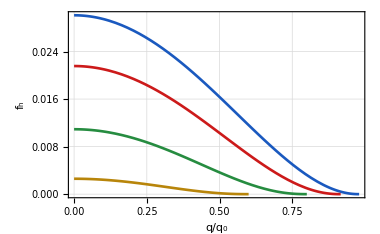

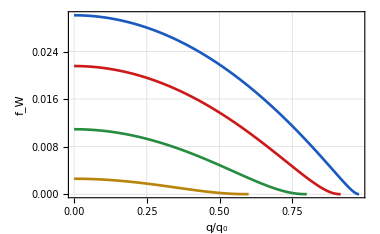

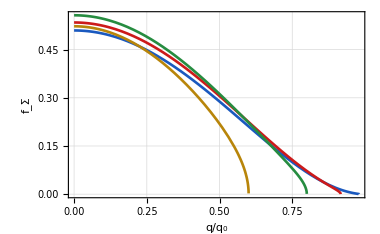

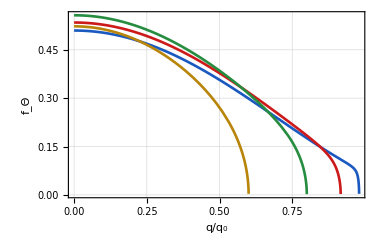

M / q_0

```mathematica
xvalues=Range[0.1,0.4,0.1]; (* 0< x <1/2*)
ξvalue = 0;

thesisColors={RGBColor[0.10,0.35,0.75],(*Blu Classico*)
RGBColor[0.80,0.10,0.10],(*Rosso*)
RGBColor[0.15,0.55,0.25],(*Verde Foresta*)
RGBColor[0.72,0.52,0.04],(*Giallo Scuro/Oro*)
RGBColor[0.45,0.15,0.55]  (*Viola/Indaco per il 5° valore*)
};

scientificPlotOptions[yLabel_]:=Sequence[PlotTheme->"Scientific",Frame->True,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],FrameLabel->{Style[Row[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],13,"Times"],Style[yLabel,14,"Times"]},PlotLabel->None,PlotLegends->None,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.92],Dashed],BaseStyle->{FontFamily->"Times",FontSize->11},FrameStyle->Directive[Black,Thickness[0.0012]],ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None];

 plotTensor=Plot[Evaluate[Table[ConditionalExpression[Funzhnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["h",Italic]]]];Print[plotTensor];

plotVector=Plot[Evaluate[Table[ConditionalExpression[FunzWnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["W",Italic]]]];Print[plotVector];

plotSigma=Plot[Evaluate[Table[ConditionalExpression[FunzΣnew[x,y,ξvalue],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Σ",Italic]]]];Print[plotSigma];

 plotTheta=Plot[Evaluate[Table[ConditionalExpression[FunzΘnew[x,y,ξvalue],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Θ",Italic]]]];Print[plotTheta]

legendStandaloneBox=Framed[Column[{Style[Row[{Style["M",Italic]," / ",Subscript[Style["q",Italic],"0"]}],12,Bold,FontFamily->"Times New Roman"],Spacer[6],LineLegend[thesisColors,Table[NumberForm[x,{2,1}],{x,xvalues}],LabelStyle->{FontFamily->"Times New Roman",FontSize->11,GrayLevel[0.15]},Spacings->{0.5,0.6},LegendMarkerSize->{20,3.5},LegendLayout->"Vertical"]},Alignment->Center],FrameStyle->Directive[GrayLevel[0.72],Thickness[0.0015]],Background->GrayLevel[0.98],RoundingRadius->4,FrameMargins->{{10,10},{8,10}} ];

Print[legendStandaloneBox]

Export[FileNameJoin[{NotebookDirectory[],"Legend_spin0.pdf"}],legendStandaloneBox];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Tensor_spin0.pdf"}],plotTensor];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Vector_spin0.pdf"}],plotVector];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Sigma_spin0.pdf"}],plotSigma];
Export[FileNameJoin[{NotebookDirectory[],"Kernel_Theta_spin0.pdf"}],plotTheta];
```

```mathematica
(* By looking in the plot below at the behaviour of Tensor and Scalar Σ kernel function, one might ask if there is a ξ for which those kernels are equals *)
```

---- Solutions -----

{{ξ→ConditionalExpression[1/90 (-(2 (15+2 √15) x^2)/(y^2-1)-√15+15), 0<x<1/2∧0<y<√(1-4 x^2)]},{ξ→ConditionalExpression[1/90 (((-30+4 √15) x^2)/(y^2-1)+√15+15), 0<x<1/2∧0<y<√(1-4 x^2)]}}

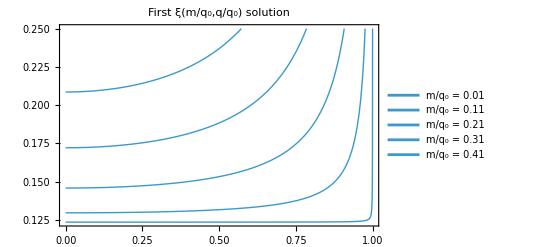

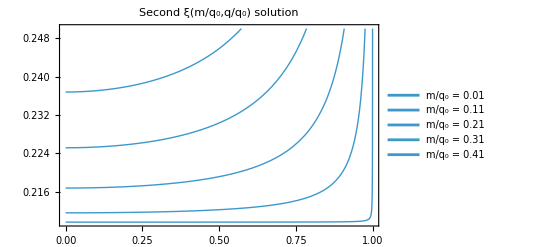

```mathematica
ΔfhΣ[x_,y_,ξ_]:=Funzhnew[x,y]-FunzΣnew[x,y,ξ]//Simplify;

(* Solve fh - fΣ = 0 *)
Print["\n ---- Solutions -----"]
solξ = Solve[ΔfhΣ[x,y,ξ]==0 &&1-y^2>=4x^2&&y>0 &&x>0,ξ]//Simplify
ξfun1[x_,y_]=ξ/.solξ[[1]];
ξfun2[x_,y_]=ξ/.solξ[[2]];

(* Plot of the solutions *)
plotξ1mass = Table[ Plot[ξfun1[x,y],{y,0,Sqrt[1-4 x^2]},PlotStyle->{Thick},PlotRange->All,Frame->True,PlotLegends->{Style[StringForm["m/q_0 = `` ",x],14]}],{x,0.01,0.499,0.1}];
Show[plotξ1mass,PlotLabel->Style[StringForm["First ξ(m/q_0,q/q_0) solution"],14],FrameLabel->{"q/q_0"}]

plotξ2mass = Table[ Plot[ξfun2[x,y],{y,0,Sqrt[1-4 x^2]},PlotStyle->{Thick},PlotRange->All,Frame->True,PlotLegends->{Style[StringForm["m/q_0 = `` ",x],14]}],{x,0.01,0.499,0.1}];
Show[plotξ2mass,PlotLabel->Style[StringForm["Second ξ(m/q_0,q/q_0) solution"],14],FrameLabel->{"q/q_0"}]
```

---- Solutions -----

{{ξ→ConditionalExpression[1/6-1/(6 √15), 0<y<1]},{ξ→ConditionalExpression[1/90 (15+√15), 0<y<1]}}

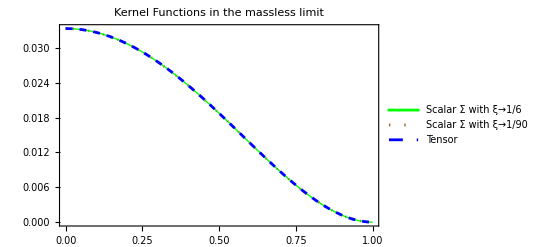

```mathematica
(* In case of massless scalar field, the ξ value (for which fh and fΣ are equals) is fixed *)

Print["\n ---- Solutions -----"]
solξmassless = Solve[ΔfhΣ[0,y,ξ]==0 &&1-y^2>=0&&y>0 ,ξ]//Simplify

FunzΣnewξ1massless[y_]=(FunzΣnew[0,y,ξ]/.solξmassless[[1]])//Simplify;
FunzΣξ2newmassless[y_]=(FunzΣnew[0,y,ξ]/.solξmassless[[2]])//Simplify;

(* Plots *)
plotΣξ1 = Plot[FunzΣnewξ1massless[y],{y,10^-5,1},PlotStyle->{Thick,Green},PlotLegends->{Style[StringForm["Scalar Σ with `` ",solξmassless[[1,1]]],14]},PlotRange->All,Frame->True];
plotΣξ2 = Plot[FunzΣξ2newmassless[y],{y,10^-5,1},PlotStyle->{Dotted,Brown},PlotLegends->{Style[StringForm["Scalar Σ with `` ",solξmassless[[2,1]]],14]},PlotRange->All,Frame->True];
plothmassless = Plot[Funzhnew[0,y],{y,10^-5,1},PlotStyle->{Dashed,Blue},PlotLegends->{"Tensor"},PlotRange->All,Frame->True];
Show[{plotΣξ1, plotΣξ2,plothmassless},PlotLabel->Style[StringForm["Kernel Functions in the massless limit"],14],FrameLabel->{"q/q_0"}]
```

```mathematica
(* Just to see, for the equivalence between the vector and scalar Σ, it does not exist a fixed ξ parameter *)
ΔfWΣ[x_,y_,ξ_]:=FunzWnew[x,y]-FunzΣnew[x,y,ξ]//Simplify;

Solve[ΔfWΣ[x,y,ξ]==0 &&1-y^2>=4x^2&&y>0&&x>0,ξ]//Simplify
Solve[ΔfWΣ[0,y,ξ]==0 &&1-y^2>=0&&y>0 ,ξ]//Simplify
```

{{ξ→ConditionalExpression[((30 √(1-y^2)+4 √15) x^2+(y^2-1) (√15-15 √(1-y^2)))/(90 (1-y^2)^(3/2)), 0<x<1/2∧0<y<√(1-4 x^2)]},{ξ→ConditionalExpression[-((4 √15-30 √(1-y^2)) x^2+(y^2-1) (15 √(1-y^2)+√15))/(90 (1-y^2)^(3/2)), 0<x<1/2∧0<y<√(1-4 x^2)]}}

{{ξ→ConditionalExpression[1/6-1/(6 √15 √(1-y^2)), 0<y<1]},{ξ→ConditionalExpression[1/90 (15+(√15)/(√(1-y^2))), 0<y<1]}}